```mathematica
multi=ResourceFunction["MultiwaySystem"]
```

[◼] | MultiwaySystem

```mathematica
getStateRenderingFunction[size_Integer]:=(Inset[ArrayPlot[{#2},ImageSize->size],#1,#3]&)
```

```mathematica
(* need to save evolved systems for easier analysis *)
```

```mathematica
show[rule_,init_,steps_,output_,stateRender_:Nothing]:=multi[CellularAutomaton[rule],init,steps,output,"StateRenderingFunction"->stateRender,ImageSize->Medium]
```

```mathematica
graph=multi[CellularAutomaton[30],CenterArray[1,5],9,"StatesGraph","StateRenderingFunction"->getStateRenderingFunction[30],ImageSize->Medium]
```

-Graphics-

```mathematica
show[30,CenterArray[1,5],9,"StatesGraph",getStateRenderingFunction[30]]
```

-Graphics-

## Finding “fixed points” in multiway CA evolution

```mathematica
Manipulate[multi[CellularAutomaton[30],CenterArray[1,5],steps,"StatesGraph","StateRenderingFunction"->getStateRenderingFunction[30]],{{steps,1,Dynamic["Steps: "<>ToString@steps]},1,10,1}]
```

## Multiway CA behavior for single rules from different classes

```mathematica
caByClass={128,22,30,110}
```

{128,22,30,110}

```mathematica
outputFunctions={"StatesGraphStructure","CausalGraphStructure","CausalInvariantQ"}
```

{StatesGraphStructure,CausalGraphStructure,CausalInvariantQ}

```mathematica
Column[Row[Function[outputFunction,multi[CellularAutomaton[#],CenterArray[1,5],5,outputFunction,ImageSize->Large]]/@outputFunctions]&/@caByClass]
```

-Graphics--Graphics-True
-Graphics--Graphics-True
-Graphics--Graphics-True
-Graphics--Graphics-True

Note: last three CA rules give true for CausalInvariantQ with 5 steps, false for 10

```mathematica
Column[Row[Function[outputFunction,multi[CellularAutomaton[#],CenterArray[1,5],5,outputFunction,ImageSize->Large]]/@outputFunctions]&/@caByClass]
```

```mathematica
Row[
multi[CellularAutomaton[#],CenterArray[1,5],10,"StatesGraph","StateRenderingFunction"->getStateRenderingFunction[30],ImageSize->Medium]&/@caByClass]
```

-Graphics--Graphics--Graphics--Graphics-

## Understanding Confluence and Causal Invariance

```mathematica
Manipulate[
Column[Function[output,Row[{output<>": ",show[22,CenterArray[1,5],steps,output,getStateRenderingFunction[30]]}]]/@outputFunctions],{steps,1,10,1}]
```

```mathematica
Manipulate[Column[{SimpleGraph[show[22,CenterArray[1,5],steps,"StatesGraph",getStateRenderingFunction[30]],ImageSize->Medium],
SimpleGraph[show[22,CenterArray[1,5],steps,"CausalGraphStructure"],ImageSize->Medium],multi[CellularAutomaton[22],CenterArray[1,5],steps,"CausalInvariantQ"]}],{steps,1,10,1}]
```

SimpleGraph::graph: A graph object is expected at position 1 in SimpleGraph[show[22,{0,0,1,0,0},8,StatesGraph,getStateRenderingFunction[30]],ImageSize→Medium].

SimpleGraph::graph: A graph object is expected at position 1 in SimpleGraph[show[22,{0,0,1,0,0},8,CausalGraphStructure],ImageSize→Medium].

```mathematica
causalInvariantRule={{1,2},{2,1}}->{{1}};
causalInvariantInit={{1,2},{2,1},{1}};ResourceFunction["MultiwaySystem"]["WolframModel"->{causalInvariantRule},{causalInvariantInit},2,"StatesGraph",VertexSize->1]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{causalInvariantRule},{causalInvariantInit},2,"CausalInvariantQ"]
```

False

## Notes

https://www.wolframscience.com/nks/notes-9-11--confluence-in-string-rewriting/
(Also considered is strong confluence—that paths can always converge in at most one step, and local confluence—that paths can converge after diverging for one step but not necessarily more.)

Most often confluence is studied in the context of terminating multiway systems—multiway systems in which eventually strings are produced to which no further replacements apply . If a terminating multiway system has the confluence property, then this implies that regardless of the path taken, a given string will always evolve to a unique string that can be thought of as giving a canonical or normal form for the original string .

https://www.wolframphysics.org/bulletins/2020/11/confluence-and-causal-invariance/
Causal Invariance : A property of multiway graphs whereby all possible paths yield the isomorphic causal graphs . When causal invariance exists, every branch in the multiway system must eventually merge . Causal invariance is a core property associated with relativistic invariance, quantum objectivity, etc . In the theory of term rewriting, a closely related property is confluence . In a terminating system, causal invariance implies that whatever path is taken, the "answer" will always be the same .

Confluence : A simplified form of causal invariance considered in term rewriting systems such as ones that reach fixed points .
A state a is deemed confluent if, for all pairs of states b, c that can be reached from a, there exists a state d that can be reached from both b and c. If every state in the system is confluent, the system itself is confluent.

A Wolfram model evolution is called causal invariant if and only if the causal graphs for singleway evolutions with any possible event ordering functions are isomorphic . Note that the definition above is only meaningful for terminating systems (i . e . the systems that always reach a "FixedPoint", a state during the evolution where no more matches can be made to its expressions) . We can then define confluence as : A Wolfram model evolution is called confluent if and only if any pair of partial singleway evolutions starting from a particular state can be continued in such a way as to reach isomorphic final states .

Before we get to specific examples, it’s essential to understand the fundamental difference between these two properties. Causal invariance has to do with symmetries between evolution branches of expressions-events graphs. It requires that, even though the branches operate on different expressions, they have the same causal structure:
-Graphics-
On the other hand, confluence has to do with the symmetries between expressions’ contents. It requires that particular states from different branches are isomorphic as hypergraphs, regardless of the causal structures that lead to them:
-Graphics-

Therefore, confluence does not imply causal invariance . Note that the "CausalInvariantQ" property of MultiwaySystem checks for confluence despite its name :

## Questions

Should I multiway systems with pieces of CA rules so they reach terminal states?

Could there be a meaningful definition of confluence for non-terminating multiway systems?

Any state can reach any other state

Measure locality of confluence by number of steps to get to given state

How can I define confluence as a measurable quantity instead of a boolean property?

Proportion of randomly chosen states that can reach one given state

Proportion of states that can be reached from all other states

What are isomorphic CA states?

Exact same state

Same state but rotated

What happens when you combine CA rules into one multiway system?

CA’s of different classes

How does a multiway system with only some parts of a CA rule behave?

Termination

Differences in confluence

Size complexity

What’s the value of studying multiway CA’s?

Perform computations by choosing which rules/replacements to apply

Machine learning based on adjusting the pool of possibilities or probabilities of different replacements by layer

Can adjust system to be terminating or non terminating

Easy to visualize

3D graph showing CA evolution in physical space and branchial space

## Next Steps

Construct CA plot from individual paths in the multiway graph

Random path

Terminal path

Paths to the same state

Construct 3D CA plot showing branchial space

Understand what CausalInvariantQ is really doing

Define confluence and causal invariance in non-terminating systems

Measure degrees of confluence

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
multi[CellularAutomaton[30],Tuples[{0,1},{5}],1,"StatesGraphStructure"]
```

-Graphics-

## Visualizing Multiway CA

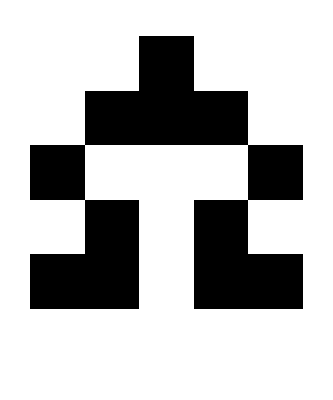
-Graphics-
Singular Rule 22 Automaton

```mathematica
Column[{ArrayPlot[CellularAutomaton[22,CenterArray[1,5],5]],Text["Singular Rule 22 Automaton"]}]
```

```mathematica
ca=CellularAutomaton[22];
```

```mathematica
init=CenterArray[1,5];
```

```mathematica
render=Inset[ArrayPlot[{#2},ImageSize->50],#1,#3]&
```